# Iteration 3: SZMR with S fighting back

## Builds on the SZMR Model

### Parameters

S → Susceptible Humans
Z → Zombies (Normal)
M → Mutant Zombies (Cannot die naturally)
R → Removed
β_z → Infection Rate by Zombies (Normal)
β_m- → Infection Rate by Mutant Zombies
α_z → Zombie  (Normal) Removal Rate
μ → Mutation Rate Z to M
κ_z → Killing of Z by S
κ_m → Killing of M by S

### Differential Equations

S^I = - β_zSZ - β_mSM
Z^I = β_zSZ - (α_z + μ)Z - κ_zSZ
M^I = β_mSM + μZ - κ_mSM
R^I = β_zSZ + β_mSM + α_zZ + κ_zSZ + κ_mSM

### Non-Dimensional Equations

S^I = - R_z0SZ - R_m0SM
Z^I = R_z0SZ - ( 1 + γ ) Z - κ_zSZ
M^I = R_m0SM + γZ - κ_mSM
R^I = R_z0SZ + R_m0SM + Z + κ_zSZ + κ_mSM

R_z0 → Basic Reproduction Rate of Zombies (Normal)
R_m0 → Basic Reproduction Rate of Mutated Zombies
γ → Dimensionless Mutation Rate

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, S, Z, M, R, t, Sf, Zf, Mf, Rf, ppSZ, ppSM, jMatrix, paramSpace, detJ, DJ, TJ, finalTJ
  },

  (* Dimensionless eq. *)
  eqns = {
    S'[t] == - Rz S[t] Z[t] - Rm S[t] M[t],
    Z'[t] == Rz S[t] Z[t] - (1 + γ) Z[t] - κz S[t] Z[t],
    M'[t] == Rm S[t] M[t] + γ Z[t] - κm S[t] M[t],
    R'[t] == Rz S[t] Z[t] + Rm S[t] M[t] + Z[t] + κz S[t] Z[t] + κm S[t] M[t]
  };

  (* Jacobian matrix *)
  jMatrix = {
    { -Rz Z - Rm M, -Rz S, -Rm S, 0},
    {  Rz Z - κz Z, Rz S - (1 + γ) - κz S, 0, 0},
    {  Rm M - κm M, γ, Rm S - κm S, 0},
    {  Rz Z + Rm M + κz Z + κm M, Rz S + 1 + κz S, Rm S + κm S, 0}
  };

  (* Trace–determinant curves *)
  paramSpace = ParametricPlot[
    {{d, 0}, {0, t}, {t^2/4, t}},
    {d, -10, 10}, {t, -10, 10},
    PlotRange -> {{-10, 10}, {-10, 10}}
  ];

  (* Solving *)
  sol = NDSolve[
    {
      eqns,
      S[0] == S0,
      Z[0] == Z0,
      M[0] == M0,
      R[0] == R0
    },
    {S, Z, M, R},
    {t, 0, tmax}
  ];

  Sf = S /. sol[[1]];
  Zf = Z /. sol[[1]];
  Mf = M /. sol[[1]];
  Rf = R /. sol[[1]];

  (* Final Trace and determinant *)
  TJ   = Tr[jMatrix];
  detJ = Det[jMatrix];

  finalTJ = TJ /. {
    S -> Sf[tmax], Z -> Zf[tmax], M -> Mf[tmax], R -> Rf[tmax],
    Rz -> Rz, Rm -> Rm, γ -> γ, κz -> κz, κm -> κm
  };

  DJ = detJ /. {
    S -> Sf[tmax], Z -> Zf[tmax], M -> Mf[tmax], R -> Rf[tmax],
    Rz -> Rz, Rm -> Rm, γ -> γ, κz -> κz, κm -> κm
  };

  (* Phase plots *)
  ppSZ = StreamPlot[
    {
      - Rz S Z - Rm S M,
        Rz S Z - (1 + γ) Z - κz S Z
    } /. M -> Mf[tmax],
    {S, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"S", "Z"},
    Frame -> True,
    FrameLabel -> {"S", "Z"}
  ];

  ppSM = StreamPlot[
    {
      - Rz S Z - Rm S M /. Z -> Zf[tmax],
        Rm S M + γ Zf[tmax] - κm S M
    },
    {S, 0, 1}, {M, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"S", "M"},
    Frame -> True,
    FrameLabel -> {"S", "M"}
  ];

  (* Trace–determinant plot*)
  detTracePlot =
    Show[
      paramSpace,
      ListPlot[{{DJ, finalTJ}}, PlotStyle -> PointSize[Large]],
      Frame -> True,
      FrameLabel -> {"Determinant", "Trace"}
    ];

  (* Outputs *)
  Row[{
    Plot[
      {Sf[t], Zf[t], Mf[t], Rf[t]},
      {t, 0, tmax},
      PlotRange -> All,
      PlotLegends -> {"S", "Z", "M", "R"},
      PlotStyle -> {
        {Green, Thick},
        {Blue, Thick},
        {Purple, Thick},
        {Gray, Thick}
      },
      AxesLabel -> {"t", "Population"},
      Frame -> True,
      FrameLabel -> {"Time (t)", "Population Fractions"},
      ImageSize -> 400
    ],
    ppSZ /. Graphics[g_, o___] :> Graphics[g, ImageSize -> 400, o],
    ppSM /. Graphics[g_, o___] :> Graphics[g, ImageSize -> 400, o],
    Show[Show[detTracePlot, ImageSize -> 600]]
  }]
 ],

  (* Sliders *)

 {{Rz, 1.0, "Normal Zombie Reproduction Number"}, 0, 3, 0.01},
 {{Rm, 1.5, "Mutant Zombie Reproduction Number"}, 0, 3, 0.01},
 {{γ,  3, "Mutation Z→M"}, 0, 5, 0.01},
 {{κz, 2, "Human killing of Z (κz)"}, 0, 3, 0.01},
 {{κm, 1, "Human killing of M (κm)"}, 0, 3, 0.01},

 {{S0, 0.65, "S(0)"}, 0, 1, 0.01},
 {{Z0, 0.35, "Z(0)"}, 0, 1, 0.01},
 {{M0, 0.0,  "M(0)"}, 0, 1, 0.01},
 {{R0, 0.0,  "R(0)"}, 0, 1, 0.01},

 {{tmax, 20, "Simulation Time"}, 1, 200, 1}
]
```

## Ensemble Simulation

### Constant Initial Conditions

S  = 650
Z = 350
M = 0
R = 0

### Base Parameters

R_z0 = 1
R_m0 = 1.5
γ  = 3
κ_z = 2

### Non-Dimensional Equations

S^I = - R_z0SZ - R_m0SM
Z^I = R_z0SZ - ( 1 + γ ) Z - κ_zSZ
M^I = R_m0SM + γZ - κ_mSM
R^I = R_z0SZ + R_m0SM + Z + κ_zSZ + κ_mSM

0 < κ_m < 3

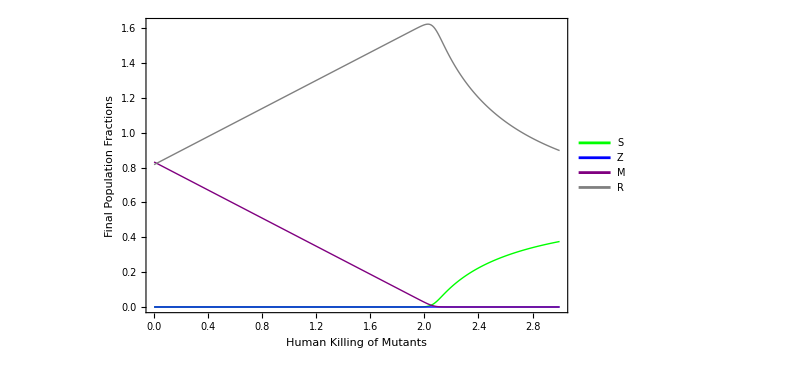

```mathematica
z = 1.0;
Rm = 1.5;
γ  = 3;
κz = 2;

finalValues =
  Table[
    Module[
      {sol, Sfunc, Zfunc, Mfunc, Rfunc, finalS, finalZ, finalM, finalR, eqns, kVal},

      kVal = k;

      eqns = {
        S'[t] == - Rz S[t] Z[t] - Rm S[t] M[t],
        Z'[t] == Rz S[t] Z[t] - (1 + γ) Z[t] - κz S[t] Z[t],
        M'[t] == Rm S[t] M[t] + γ Z[t] - kVal S[t] M[t],
        R'[t] == Rz S[t] Z[t] + Rm S[t] M[t] + Z[t] + κz S[t] Z[t] + kVal S[t] M[t]
      };

      sol = NDSolve[
        {
          eqns,
          S[0] == 650./1000.,
          Z[0] == 350./1000.,
          M[0] == 0.,
          R[0] == 0.
        },
        {S, Z, M, R},
        {t, 0, 100}
      ];

      Sfunc = S /. sol[[1]];
      Zfunc = Z /. sol[[1]];
      Mfunc = M /. sol[[1]];
      Rfunc = R /. sol[[1]];

      finalS = Sfunc[100.];
      finalZ = Zfunc[100.];
      finalM = Mfunc[100.];
      finalR = Rfunc[100.];

      {kVal, finalS, finalZ, finalM, finalR}
    ],
    {k, 0.0, 3.0, 0.01}   (* vary κm *)
  ];

kappaMValues = finalValues[[All, 1]];
finalSValues = finalValues[[All, 2]];
finalZValues = finalValues[[All, 3]];
finalMValues = finalValues[[All, 4]];
finalRValues = finalValues[[All, 5]];

ListLinePlot[
  {
    Transpose[{kappaMValues, finalSValues}],
    Transpose[{kappaMValues, finalZValues}],
    Transpose[{kappaMValues, finalMValues}],
    Transpose[{kappaMValues, finalRValues}]
  },
  PlotRange -> All,
  PlotStyle -> {
    {Green, Thick}, (* S *)
    {Blue, Thick}, (* Z *)
    {Purple, Thick}, (* M *)
    {Gray, Thick} (* R *)
  },
  Frame -> True,
  ImageSize -> 600,
  FrameLabel -> {"Human Killing of Mutants", "Final Population Fractions"},
    Frame -> True,
  PlotLegends -> {
    "S", "Z", "M", "R",
   }
]
```